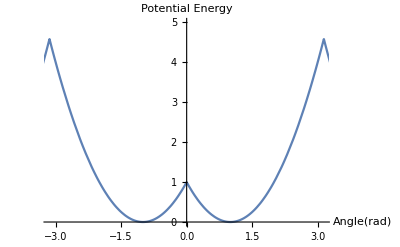

```mathematica
Plot[(ArcCos[Cos[theta]]-t0)^2/.t0->1,{theta,-2 π,2 π},Axes->True,AxesLabel->{"Angle(rad)","Potential Energy"},PlotRange->{{-π,π},{0,5}}]
```

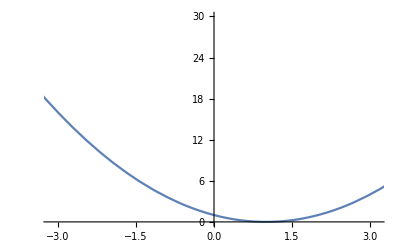

```mathematica
Plot[(theta-t0)^2/.t0->1,{theta,-2 Pi,2 Pi},PlotRange->{{-Pi,Pi},{0,30}}]
```

```mathematica
ArcCos[Cos[3Pi/4]]
```

(3 π)/4

```mathematica
ArcCos[Cos[-3*Pi/4]]
```

(3 π)/4

```mathematica
Pi+ArcCos[Cos[-3*Pi/4]]
```

(7 π)/4

```mathematica
dot=x1*x2+y1*y2+z1*z2;
lenSq1=x1*x1+y1*y1+z1*z1;
lenSq2=x2*x2+y2*y2+z2*z2;
angle=ArcCos[dot/Sqrt(lenSq1*lenSq2)];
```

```mathematica
x1=1;y1=0;z1=0;
x2=0;y2=1;z2=0;
```

```mathematica
cross={y1*z2-z1*y2,z1*x2-x1*z2,x1*y2-y1*x2}
```

{0,0,1}

```mathematica
v1={1,0,0};
v2={0.01,-1,0};
Dot[v2,v1]
```

0.01

```mathematica
Wedge[v1,v2]
```

{1.,0.,0.}⋀{0.01,-1.,0.}

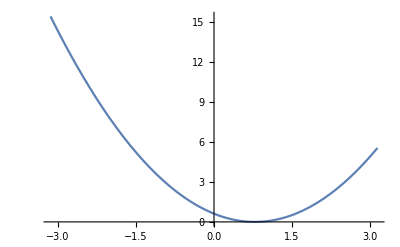

```mathematica
Plot[If[Sin[theta]<0,(Pi+ArcCos[Cos[theta]]-t0)^2,(ArcCos[Cos[Pi-theta]]-t0)^2]/.t0->3*Pi/4,{theta,-Pi,Pi}]
```

```mathematica
Plot[If[theta<0,(Pi+ArcCos[Cos[theta]]-t0)^2,(ArcCos[-Cos[theta]]-t0)^2]/.t0->3Pi/4,{theta,-Pi,Pi}]
```

-Graphics-

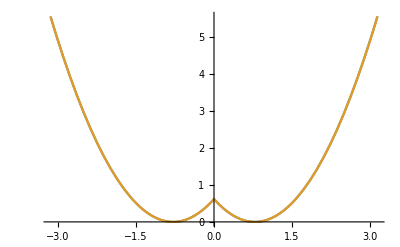

```mathematica
Plot[{(ArcCos[Cos[Pi-theta]]-3Pi/4)^2,(ArcCos[-Cos[theta]]-3Pi/4)^2},{theta,-Pi,Pi}]
```

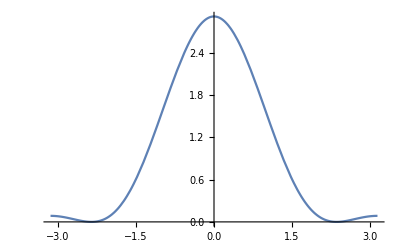

```mathematica
Plot[{(Cos[theta]-Cos[3Pi/4])^2},{theta,-Pi,Pi}]
```

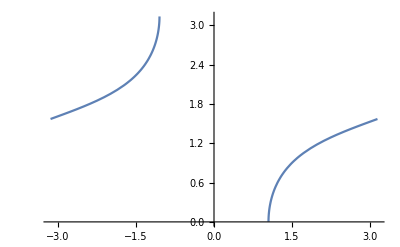

```mathematica
ft = (Cos[theta1]*Cos[theta2]+Cos[theta3])/(Sin[theta1]*Sin[theta2]);
Plot[ArcCos[ft]/.{theta2->Pi/3,theta3->Pi/3},{theta1,-Pi,Pi}]
```